# Visualizing Data

```mathematica
{1,4,9,16,25}
```

{1,4,9,16,25}

```mathematica
data = %
```

{1,4,9,16,25}

```mathematica
data
```

{1,4,9,16,25}

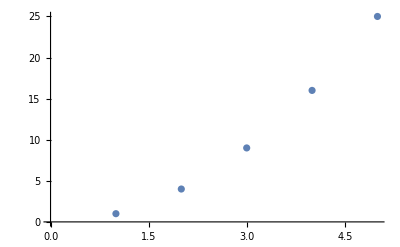

```mathematica
ListPlot[data]
```

WolframAlphaQueryParseResults

-Graphics-

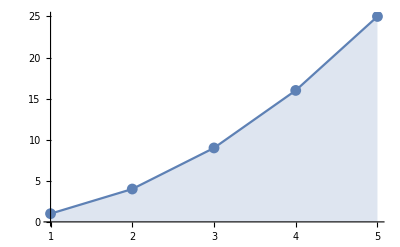

```mathematica
ListLinePlot[data, Mesh->All,
Filling->Axis,
AxesOrigin->{1,0}]
```

```mathematica
Manipulate[
lplot[data],
{lplot, {ListPlot,ListLinePlot,ListLogPlot,ListLogLogPlot}},
Initialization:>(data)]
```

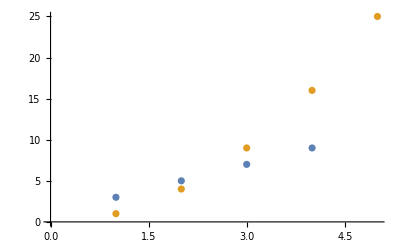

```mathematica
ListPlot[{{3,5,7,9},{1,4,9,16,25}}]
```

```mathematica
dataset1 = {1,4,9,16,25}
```

{1,4,9,16,25}

```mathematica
dataset2 = {3,5,7,8}
dataset3 = {2,5,9,14,20}
```

{3,5,7,8}

{2,5,9,14,20}

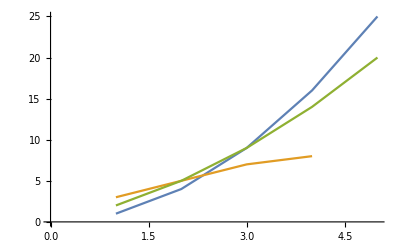

```mathematica
ListLinePlot[{dataset1,dataset2,dataset3}]
```

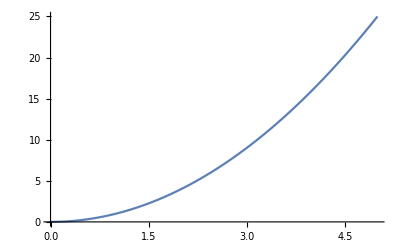

```mathematica
Plot[x^2,{x,0,5}]
```

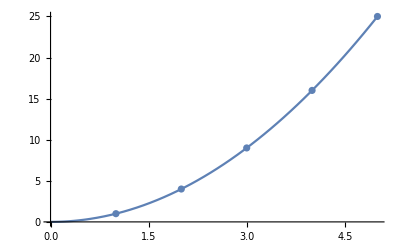

```mathematica
Show[Plot[x^2,{x,0,5}],ListPlot[{1,4,9,16,25}]]
```

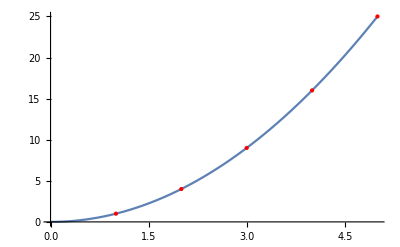

```mathematica
Show[Plot[x^2,{x,0,5}],ListPlot[{1,4,9,16,25},
PlotStyle->{Red,PointSize[Medium]}]]
```

```mathematica
ListPlot[{1,4,9,16,25}]
```

-Graphics-

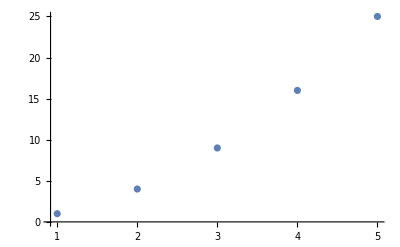

```mathematica
ListPlot[{{1,1},{2,4},{3,9},{4,16},{5,25}}]
```

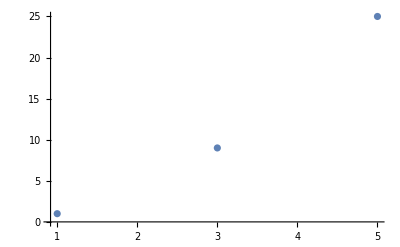

```mathematica
ListPlot[{{1,1},{3,9},{5,25}}]
```

```mathematica
ListPlot[{{3,9},{1,1},{5,25}}]
```

-Graphics-

```mathematica
dataset1={{1,1},{2,4},{3,9},{4,16},{5,25}};dataset2={{1,3},{2,5},{3,7},{4,9}};dataset3={{1,2},{2,5},{3,9},{4,14},{5,20}};
```

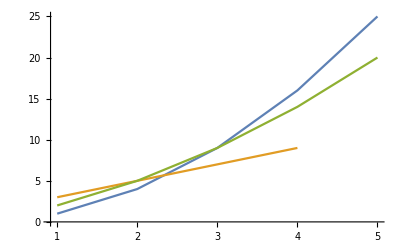

```mathematica
ListLinePlot[{dataset1,dataset2, dataset3}]
```

```mathematica
dataset4 = {100,12,24,46}
```

{100,12,24,46}

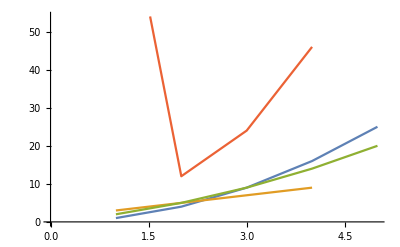

{1,2,3,5}

```mathematica
ListLinePlot[{dataset1,dataset2,dataset3,dataset4}]
```

```mathematica
Table[Prime[n],{n,5}]
```

{2,3,5,7,11}

```mathematica
Manipulate[
ListLinePlot[Table[{n,Prime[n]},{n,1,max,1}],PlotRange->{{0,50},{0,250}}],
{max,1,50,1}]
```

## Visualize a Three-Dimensional List of Numbers

```mathematica
data3 = Table[N[Sin[x]Cos[y]],
{x,-3,3,0.1},
{y,-3,3,.1}];
```

```mathematica
ListPlot3D[data3]
```

-Graphics3D-

```mathematica
ListPointPlot3D[data3]
```

-Graphics3D-

```mathematica
Manipulate[
func[Table[N[Sin[x]Cos[y], 10], {x,-3,3, incr},{y,-3,3}]],
{{incr, 1, "step size"}, 1, 0.05},
{{func,ListPlot3D, "function"}, {ListPlot3D,ListPointPlot3D}}]
```